```mathematica
QIntegral[weights_,abscissas_,f_]:=Sum[weights[[i]]f[abscissas[[i]]],{i,1,Length[weights]}]
```

```mathematica
FrobeniusNorm[matrix_]:=Sqrt[Total[matrix^2,2]]
```

```mathematica
FrobeniusNorm2[matrix_]:=Total[matrix^2,2]
```

```mathematica
BesselJDerivativeZero[i_]:=BesselJZero[1,i-1]
BesselJDerivativeZero[1]:=0
```

```mathematica
ExpectedDirichletQuadrature[Nmax_]:=ExpectedDirichletQuadrature[Nmax,BesselJZero[0,Nmax+1]]
ExpectedDirichletQuadrature[Nmax_,S_]:=Transpose[Table[{2/S^2 1/BesselJ[1,BesselJZero[0,i1]]^2,BesselJZero[0,i1]/S},{i1,1,Nmax}]]
```

```mathematica
DiscreteOrthogonalityMatrix[quadrature_]:=DiscreteOrthogonalityMatrix[quadrature,Length[quadrature[[1]]]]
DiscreteOrthogonalityMatrix[quadrature_,Nmax_]:=Module[{weights=quadrature[[1]],abscissas=quadrature[[2]]},Table[QIntegral[weights,abscissas,2/Abs[BesselJ[0,BesselJDerivativeZero[i2]]BesselJ[0,BesselJDerivativeZero[i3]]] BesselJ[0,BesselJDerivativeZero[i2]#]BesselJ[0,BesselJDerivativeZero[i3]#]&],{i2,1,Nmax},{i3,1,Nmax}]]
```

```mathematica
TestSearch[Nmax_,precision_]:=Module[{weights=Table[Unique[w],{iw,1,Nmax}],abscissas=Table[Unique[x],{ix,1,Nmax}],initialQuadrature=Evaluate[ExpectedDirichletQuadrature[Nmax,N[BesselJZero[0,Nmax+1],precision]]]},Module[{err},err[w_?(VectorQ[#,NumericQ]&),x_?(VectorQ[#,NumericQ]&)]:=FrobeniusNorm[DiscreteOrthogonalityMatrix[{w,x},Nmax]-IdentityMatrix[Nmax]];soln=FindMinimum[err[weights,abscissas],Flatten[Table[{{weights[[i10]],initialQuadrature[[1,i10]]},{abscissas[[i10]],initialQuadrature[[2,i10]]}},{i10,1,Nmax}],1],WorkingPrecision->2precision,MaxIterations->10000];{soln[[1]],{weights,abscissas}/.soln[[2]]}]]
```

```mathematica
TestQuadrature[Nmax_]:={Table[Unique[w],{iw,1,Nmax}],Table[Unique[x],{ix,1,Nmax}]}
```

```mathematica
TestQuadrature[4]
```

{{w$1553,w$1554,w$1555,w$1556},{x$1557,x$1558,x$1559,x$1560}}

```mathematica
Simplify@FrobeniusNorm[DiscreteOrthogonalityMatrix[Out[14]]-IdentityMatrix[4]]
```

√((-1+2 w$1349+2 w$1350+2 w$1351+2 w$1352)^2+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,1]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,1]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,1]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,1]])^2)/BesselJ[0,BesselJZero[1,1]]^2+(-BesselJ[0,BesselJZero[1,1]]^2+2 w$1349 BesselJ[0,x$1353 BesselJZero[1,1]]^2+2 w$1350 BesselJ[0,x$1354 BesselJZero[1,1]]^2+2 w$1351 BesselJ[0,x$1355 BesselJZero[1,1]]^2+2 w$1352 BesselJ[0,x$1356 BesselJZero[1,1]]^2)^2/BesselJ[0,BesselJZero[1,1]]^4+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,2]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,2]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,2]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,2]])^2)/BesselJ[0,BesselJZero[1,2]]^2+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,1]] BesselJ[0,x$1353 BesselJZero[1,2]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,1]] BesselJ[0,x$1354 BesselJZero[1,2]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,1]] BesselJ[0,x$1355 BesselJZero[1,2]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,1]] BesselJ[0,x$1356 BesselJZero[1,2]])^2)/(BesselJ[0,BesselJZero[1,1]]^2 BesselJ[0,BesselJZero[1,2]]^2)+(-BesselJ[0,BesselJZero[1,2]]^2+2 w$1349 BesselJ[0,x$1353 BesselJZero[1,2]]^2+2 w$1350 BesselJ[0,x$1354 BesselJZero[1,2]]^2+2 w$1351 BesselJ[0,x$1355 BesselJZero[1,2]]^2+2 w$1352 BesselJ[0,x$1356 BesselJZero[1,2]]^2)^2/BesselJ[0,BesselJZero[1,2]]^4+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,3]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,3]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,3]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,3]])^2)/BesselJ[0,BesselJZero[1,3]]^2+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,1]] BesselJ[0,x$1353 BesselJZero[1,3]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,1]] BesselJ[0,x$1354 BesselJZero[1,3]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,1]] BesselJ[0,x$1355 BesselJZero[1,3]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,1]] BesselJ[0,x$1356 BesselJZero[1,3]])^2)/(BesselJ[0,BesselJZero[1,1]]^2 BesselJ[0,BesselJZero[1,3]]^2)+(8 (w$1349 BesselJ[0,x$1353 BesselJZero[1,2]] BesselJ[0,x$1353 BesselJZero[1,3]]+w$1350 BesselJ[0,x$1354 BesselJZero[1,2]] BesselJ[0,x$1354 BesselJZero[1,3]]+w$1351 BesselJ[0,x$1355 BesselJZero[1,2]] BesselJ[0,x$1355 BesselJZero[1,3]]+w$1352 BesselJ[0,x$1356 BesselJZero[1,2]] BesselJ[0,x$1356 BesselJZero[1,3]])^2)/(BesselJ[0,BesselJZero[1,2]]^2 BesselJ[0,BesselJZero[1,3]]^2)+(-BesselJ[0,BesselJZero[1,3]]^2+2 w$1349 BesselJ[0,x$1353 BesselJZero[1,3]]^2+2 w$1350 BesselJ[0,x$1354 BesselJZero[1,3]]^2+2 w$1351 BesselJ[0,x$1355 BesselJZero[1,3]]^2+2 w$1352 BesselJ[0,x$1356 BesselJZero[1,3]]^2)^2/BesselJ[0,BesselJZero[1,3]]^4)

```mathematica
InitialGuess[quadrature_]:=Transpose[{Flatten@quadrature,Flatten@ExpectedDirichletQuadrature[Length[quadrature[[1]]]]}]
```

```mathematica
Out[14]
```

{{w$1349,w$1350,w$1351,w$1352},{x$1353,x$1354,x$1355,x$1356}}

```mathematica
InitialGuess[Out[14]]
```

{{w$1349,2/(BesselJ[1,BesselJZero[0,1]]^2 BesselJZero[0,5]^2)},{w$1350,2/(BesselJ[1,BesselJZero[0,2]]^2 BesselJZero[0,5]^2)},{w$1351,2/(BesselJ[1,BesselJZero[0,3]]^2 BesselJZero[0,5]^2)},{w$1352,2/(BesselJ[1,BesselJZero[0,4]]^2 BesselJZero[0,5]^2)},{x$1353,BesselJZero[0,1]/BesselJZero[0,5]},{x$1354,BesselJZero[0,2]/BesselJZero[0,5]},{x$1355,BesselJZero[0,3]/BesselJZero[0,5]},{x$1356,BesselJZero[0,4]/BesselJZero[0,5]}}

```mathematica
TestSearch[Nmax_,precision_]:=Module[{quadrature=TestQuadrature[Nmax]},soln=FindMinimum[Evaluate[FrobeniusNorm[DiscreteOrthogonalityMatrix[quadrature]-IdentityMatrix[Nmax]]],Evaluate[InitialGuess[quadrature]],WorkingPrecision->precision,MaxIterations->100000];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
TestSearch2[Nmax_,precision_]:=Module[{quadrature=TestQuadrature[Nmax]},soln=FindMinimum[Evaluate[FrobeniusNorm2[DiscreteOrthogonalityMatrix[quadrature]-IdentityMatrix[Nmax]]],Evaluate[InitialGuess[quadrature]],WorkingPrecision->precision,MaxIterations->100000];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
TestSearch[Nmax_]:=TestSearch[Nmax,MachinePrecision]
```

```mathematica
TestSearch3[Nbasis_,Nx_,precision_]:=Module[{quadrature=TestQuadrature[Nx]},soln=FindMinimum[Evaluate[FrobeniusNorm2[DiscreteOrthogonalityMatrix[quadrature, Nbasis]-IdentityMatrix[Nbasis]]],Evaluate[InitialGuess[quadrature]],WorkingPrecision->precision,MaxIterations->100000];{soln[[1]],quadrature/.soln[[2]]}]
```

```mathematica
TestSearch3[4,4,40]
```

{7.321464923617369219822645056385062426406×10^-12,{{0.04815739182077047570776965434417482338186,0.1088893874340669552570749561535464821441,0.157967523479510768991646892023652390232,0.1849855005206070312952852095473246486458},{0.1939997033593015396899515076751140281011,0.4423429472939028456681684663008799979047,0.6823638067128266132468388844743684512907,0.9009300826436743365663419660746803760374}}}

```mathematica
TestSearch3[4,5,40]
```

{4.975136253549467764319642313691523229384×10^-15,{{0.04194196185963130303584034172887237829174,0.09348062465941796499239290665332820326905,0.1326935854140274506379187391727991923252,0.1458180560335814473529594450040021067739,0.08606579155584427343173242875043612236272},{0.1812053548222375258401177928435100447444,0.4116769481065474165969757618837428444355,0.6313938742199370131246101367825642384189,0.8264266352986527847368248651841984881527,1.03055329747379248259376334078099708311}}}

```mathematica
TestSearch3[4,5,40]
```

{4.975136253549467764319642313691523229384×10^-15,{{0.04194196185963130303584034172887237829174,0.09348062465941796499239290665332820326905,0.1326935854140274506379187391727991923252,0.1458180560335814473529594450040021067739,0.08606579155584427343173242875043612236272},{0.1812053548222375258401177928435100447444,0.4116769481065474165969757618837428444355,0.6313938742199370131246101367825642384189,0.8264266352986527847368248651841984881527,1.03055329747379248259376334078099708311}}}

```mathematica
TestSearch3[4,5,50]
```

{4.9751362535494677643196423136915580010514511518348×10^-15,{{0.041941961859631303035852504427663538811556962338733,0.093480624659417964992428252968449146493527676246769,0.13269358541402745063800834471818370286303582428122,0.14581805603358144735326451750318110457289062034926,0.086065791555844273431290241698060816753135558328274},{0.1812053548222375258401433270966798154900589623129,0.41167694810654741659704189465584669513606374145935,0.63139387421993701312474470831402237898411352985306,0.82642663529865278473713233775166002354098788854501,1.0305532974737924825930256088417182700700887905538}}}

```mathematica
TestSearch3[4,5,60]
```

{4.97513625354946776431964231369155800105144960804293482419879×10^-15,{{0.0419419618596313030358525055248817513515586992108828723667329,0.0934806246594179649924282561954466614734793360406389080018702,0.13269358541402745063800835304967541459238580785046009745821,0.145818056033581447353264546195688287348111380426937984664852,0.0860657915558442734312902003498474736182594101407121340505879},{0.181205354822237525840143329396991589839693341316480154878963,0.411676948106547416597041900651303508387049752621642707494686,0.631393874219937013124744720660060370065125080104927419735746,0.826426635298652784737132366366986245301144789859765583328644,1.03055329747379248259302553966970568352279413880912738691474}}}

```mathematica
TestSearch3[4,6,50]
```

{6.243425453790609691832552297154593575076715940486×10^-63,{{0.018906717598850532062381183394564294052185957322691,0.032970932278516399694190864827608589197726110773113,0.079497657775236690370078066299836063408642323403402,0.1155287373308019261308135667111967966587123494224,0.13054601359741342108091429347575886779233168459966,0.12254994141918103066162202529100934596194025273777},{0.13046851509924068597578947140189061177774411716422,0.25361368529941379859520618045206960390084516885772,0.41934385729535467193032648565814333093859573237574,0.61138267111629938169569699233129233755641608286943,0.78994575392979720836072605347455057166698860991267,0.93775553248892146481268704214207419104088889069996}}}

```mathematica
TestSearch3[4,6,60]
```

{6.82102653631869740159510295797648222953373137884725807027643×10^-73,{{0.0189896747554704997916016608980020961526209194068174551827974,0.0327044637526859885727403881743568974858400810994366938468114,0.0795027137229103182003654257897141368512118494119948433973034,0.115579360335668044670557166333612833894085995438465092902575,0.130608992411254047764701556856697546471388904081564912597727,0.122614795022011101000033801947616488897188455213143942238458},{0.130895814901164826451766240157036923821493918850437418967545,0.253329695595901241709706222856909169062626268864258846266747,0.418892215935834696435017829176502169583406571585008450358572,0.611129604197564028072402329579150104678769751025775737509909,0.789823092391759882002088513051100456351340426528379920343539,0.937720937621690611846782196422513280515178646730109871840338}}}

```mathematica
TestSearch3[4,5,30]
```

{4.97513625354946776431980627434×10^-15,{{0.0419419618596313026498854443184,0.0934806246594179645601064174279,0.132693585414027452253455039467,0.145818056033581458733533855279,0.0860657915558442612538764118963},{0.181205354822237524972723076927,0.411676948106547415028819771506,0.631393874219937012559645720958,0.826426635298652790759882047919,1.03055329747379245889770073254}}}

```mathematica
TestSearch3[4,6,80]
```

$Aborted

```mathematica
TestSearch3[3,3,120]
```

{2.15250019751830409460163757475216028453172908940002046392778353870778787686813197386426296492217819346091465909149086307×10^-128,{{0.0830790361815195463698618261472538265423524007819261706148661549653479730166412263516951387450554205879120305931844476691,0.178889028330110165517002319534961910054324800706502153832289427940423909733270144543341511897118953619605723061852227572,0.238031935488370288113135854317784263403322798511571675552844417094228117250088629104963349357825625792482246344963324759},{0.255389235014544403471838897256767793483508331192538520845086913900488502501247858458865158118370532769907978470737681866,0.575926445456361605297178008729595422473343686045023298595788714629584482339276191652039503840468156604493996682908551503,0.868709935851650762129166179665300624711467759631193391036441224394996563329243268145545799343932975636682542110961892365}}}

```mathematica
TestSearch3[5,7,30]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{1.46472645425006007536164353407×10^-18,{{0.01180816076244815123845415444,0.0358145250372293785423487262021,0.0621627404355998500443881170396,0.0858507285244733727256635615162,0.1024744472549835436473698585,0.106238402358631663890932134608,0.0956509955151106731691437433852},{0.0920980816575588050564114255536,0.234568214383969912573001350275,0.391307997898347761340552098853,0.54945988312761043300064754556,0.701323200869098509179673586669,0.838583499742039913029997870732,0.952004782104891588172808403098}}}

```mathematica
TestSearch3[5,7,40]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{2.321721897375371335474014638070839516502×10^-18,{{0.012023306008287970401472107620630010666,0.03466448779813142822452880494584714149349,0.06083008835510346611387585427724201582534,0.08527569198044890710130864421847663032673,0.1028314637835646654400028056114544134296,0.1073120787767076886370189480398775498367,0.09706288316041960800346468067717094037431},{0.09426790341359436746777156093080550923159,0.2333677569032128942495793749939124242016,0.387094525889569189543616360118723346071,0.5446452748057002349175744882783877519106,0.6974100473380806372950429284173945700176,0.8362032257083790984183708888997384223072,0.9512463190882707378976800631480387653226}}}

```mathematica
TestSearch3[5,8,30]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{2.55956166287484225562452571734×10^-9,{{0.00997287153325784200059477514284,0.0224720927374803134132820745697,0.0363540255729490612614404706031,0.0486963880625024141191339829302,0.0629190345445572220864808797332,0.0782066214020501639765439312017,0.0989136565327517819516379040125,0.14245559066698104659816392322},{0.0868683513437531915683425875479,0.20189825749864371207813335465,0.313477995772530876855621075913,0.430394607361373162551257778155,0.542264084282081050343857971864,0.661900628990225270533583275933,0.780493463758617123666848529776,0.92268478019667269365175566542}}}

```mathematica
FindMinimum[Evaluate[Out[15]],Evaluate[InitialGuess[Out[14]]]]
```

$Aborted

```mathematica
Timing@TestSearch[4,40]
```

{4.46311,{2.705820563824838925237757128353541182839×10^-6,{w$495397→0.04815739182077047570778774580434339423776,w$495398→0.1088893874340669552571183408053488035777,w$495399→0.1579675234795107689916901943601553543806,w$495400→0.184985500520607031295180543869500347217,x$495401→0.193999703359301539689987533252696996717,x$495402→0.4423429472939028456682538431503920056572,x$495403→0.6823638067128266132469661532506434371567,x$495404→0.9009300826436743365664209187863308414671}}}

```mathematica
TestSearch2[10,40]
```

{3.348794336710968359396834600408580354973×10^-11,{{0.007773279210521646366396620812369046002071,0.01808062256912812082603275820511861851411,0.02836511485079881300466399397092296410414,0.03857599315282231578783094291960190453858,0.04864463611304265423113662988567067283272,0.05842936284477802645798274319613003357348,0.06759477539950151290204943303071483876634,0.07525561414530545002616114229330037586804,0.07918003578952574986754956307493484994005,0.07810052934747536822457817332346012080631},{0.07783599368265654287783372586555947501145,0.1786319073778422869677882457437999297821,0.2799347561549564122383672303507374034061,0.3812102541882085153269984860744539136021,0.4822593259600674936014639652691536988788,0.5828501065226657354111330186170366656569,0.6825607497046134148152009656293585854193,0.7804616804109562906959461133419443047758,0.8743301043182833740844023592797741338644,0.9602599572596595319965079881974935663042}}}

```mathematica
Total[(DiscreteOrthogonalityMatrix[Out[15][[2]],20][[11,1;;10]])^2]
```

0.49120751406503436708693888719245497549

```mathematica
ExcessNorm[Nmax_,Nadditional_]:=Module[{matrix=DiscreteOrthogonalityMatrix[TestSearch2[Nmax,40][[2]],Nmax+Nadditional]},Table[Total[matrix[[Nmax+i,1;;10]]^2],{i,1,Nadditional}]]
```

```mathematica
ExcessNorm[10,10]
```

{0.49120751406503436708693888719245497549,0.7505244874526297089536278010487733924,0.878808023000118010204199911893318471,0.943173441409005531813572625128213197,0.976845126416758323037518386166699635,0.996685382739825107904908124444235698,1.01222888961570462296938205717826591,1.0317604103010338808814305782302588,1.07469705121150981326916903350484475,1.385846935537280044727139967974009341}

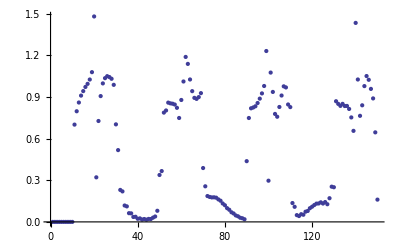

```mathematica
ListPlot[ExcessNorm[20,150]]
```

```mathematica
Timing@TestSearch[10,40]
```

{145.873,{5.786876823219039590997042348974640677778×10^-6,{{0.007773279210521646366409789492170019235247,0.01808062256912812082606458102131838373239,0.02836511485079881300471759152311145684981,0.03857599315282231578791212748244793822079,0.04864463611304265423125554217131589976375,0.05842936284477802645815645316577430065293,0.06759477539950151290230274021676931105392,0.07525561414530545002649540619547344006469,0.07918003578952574986767317656632199354236,0.07810052934747536822339530361171163692684},{0.07783599368265654287789936662836541230683,0.1786319073778422869679417905039091720567,0.2799347561549564122386165172976353176226,0.3812102541882085153273566674923970045777,0.4822593259600674936019522948974712929644,0.5828501065226657354117850264623394369401,0.6825607497046134148160673254147105999843,0.7804616804109562906970853057325357452753,0.8743301043182833740857449010114511799642,0.9602599572596595319972694333594062506471}}}}

```mathematica
Timing@TestSearch2[5,40]
```

{4.79944,{2.043677940877138033874884189089926213479×10^-11,{{0.03113217003440892508479716057349703417544,0.07157699755069691620228688463541673150879,0.1089424878057284182160644578820580820843,0.1374192121790945166457374413198151857249,0.1509289239486615420253850286334470056787},{0.1558608482554140009506773498306520256783,0.356725209419088713776307960187775766651,0.5555284784988187259555062485199439805105,0.7464784769935946565343932771565311706333,0.9205569514457777645612697257092988551379}}}}

```mathematica
Sqrt[2.043677940877138033874884189089926213478659674749356006133862849385`40.*^-11]
```

4.520705631731774275662116021150244140577×10^-6

```mathematica
Timing@TestSearch2[10,40]
```

{7.98653,{3.348794336710968359396834600408580354973×10^-11,{{0.007773279210521646366396620812369046002071,0.01808062256912812082603275820511861851411,0.02836511485079881300466399397092296410414,0.03857599315282231578783094291960190453858,0.04864463611304265423113662988567067283272,0.05842936284477802645798274319613003357348,0.06759477539950151290204943303071483876634,0.07525561414530545002616114229330037586804,0.07918003578952574986754956307493484994005,0.07810052934747536822457817332346012080631},{0.07783599368265654287783372586555947501145,0.1786319073778422869677882457437999297821,0.2799347561549564122383672303507374034061,0.3812102541882085153269984860744539136021,0.4822593259600674936014639652691536988788,0.5828501065226657354111330186170366656569,0.6825607497046134148152009656293585854193,0.7804616804109562906959461133419443047758,0.8743301043182833740844023592797741338644,0.9602599572596595319965079881974935663042}}}}

```mathematica
Timing@TestSearch2[15,40]
```

{104.632,{2.240688840075094417406965489360073034458×10^-11,{{0.003429367525699581048362078973275832957507,0.007981701635350555032030628769192527895964,0.01253770536019758854436485384301642368653,0.01708895537527439746362519934324742633245,0.02163188663264872605052302478933463828043,0.02616184079172017510594805316341743352657,0.03067156720735084460531499858212194839878,0.0351488861499947867315964712914019772612,0.0395718615482854957779170400693611692651,0.04389779280840275013081415732549396251323,0.04803560594335814919138297896688129590995,0.05176955905475205710372113827830389159042,0.05453779143484160798398268185942122729711,0.05497420697225464652030570712952289092473,0.05256127737470492629335083323627040074873},{0.05169757278719585873534173113356978224686,0.1186630288389700786026431153754953886787,0.1860128995277087886237385612434385842125,0.2534335005254614151689430405020791119507,0.3208599380979844395481708626170650996755,0.3882621374368824285237331794911097347462,0.4556150535974060947464643660975985062872,0.522888463621743535658163928277253276609,0.5900379661641576471928923274164259699513,0.656990133903671968487283621236020650337,0.723611050305501386499212109665524685703,0.7896302321149127451328258652115449806294,0.8544389149391005333972811652056995161685,0.9165848530206465969130377020220121824761,0.9735500487818646392197275026098858297328}}}}

```mathematica
Timing@TestSearch2[30,30]
```

{60.0792,{7.45345948014358330461170983013×10^-12,{{0.000847892769366777992734962591803,0.0019737145814595237719259165584,0.00310115874664974928224510465178,0.00422867566532193116326755652852,0.00535611978765808848019878036964,0.00648343728626024229190950953276,0.00761058426076930880817532361673,0.00873751357419204965693251259256,0.00986417010005529786662395551242,0.0109904869915765131369790619795,0.0121163813298076026785385518317,0.0132417483406122626726566784469,0.0143664533331161426986676981195,0.0154903201483691444818327134187,0.0166131142173766793527056050987,0.0177345171197028492569000452108,0.0188540873910522057524415559098,0.0199711984102092452912537961375,0.0210849367602761698637546284003,0.0221939297332580786804814135562,0.0232960400294818475482709182508,0.0243877984111982216570975423175,0.0254632874785589728677246978496,0.0265117929786294698362113793006,0.027512456114971632587361089828,0.0284209467553451254961127500396,0.029133055809257391066443303552,0.0293814351834504584482723905029,0.0285390728800144986769802316972,0.0264936851639757137378940941325},{0.025705736259411819098418135984,0.0590052537180734017893550840194,0.0925010930622963724633345150061,0.126040836207150812814020629104,0.159596695302423947100795487301,0.193159744728531854635507428615,0.226726135859111155945492040601,0.260293832176154788718571899016,0.293861554702853063394393671504,0.327428363661006001834512236949,0.360993462508153856015754373678,0.394556089302902670873797055214,0.428115443181862992249913313128,0.461670621916950745128307068205,0.495220556469555476205818346674,0.528763930970547423122141266791,0.562299074817363508124052326762,0.59582380778788373176491549704,0.629335207341245444838673603868,0.662829244809959966522919655925,0.696300193321407549982100047817,0.729739620842548292679634326024,0.763134588872455713198741369011,0.79646423294053514834015042812,0.829692796166085162991245259235,0.862754199077060940678297173637,0.895514483173094988787568057252,0.927672571908964266620348822267,0.958514297199513658368750593647,0.98681380799347285870482467039}}}}

```mathematica
Timing@TestSearch2[30,MachinePrecision]
```

$Aborted

```mathematica
TestQuadrature[3]
```

{{w$1028695,w$1028696,w$1028697},{x$1028698,x$1028699,x$1028700}}

```mathematica
D[FrobeniusNorm2[DiscreteOrthogonalityMatrix[Out[58]]-IdentityMatrix[3]],{Evaluate[Flatten[Out[58]]]}]
```

```mathematica
Timing@TestSearch4[4,30]
```

{1.90168,{7.32146492361736921982264557467×10^-12,{{0.0481573918207704756117347282789,0.108889387434066955026776189501,0.157967523479510768761785084105,0.184985500520607031850882246097},{0.193999703359301539498716887573,0.442342947293902845214962402982,0.682363806712826612571257766331,0.900930082643674336147237143264}}}}

```mathematica
Timing@TestSearch2[4,30]
```

{1.4586,{7.32146492361736921982264557467×10^-12,{{0.0481573918207704756117347282789,0.108889387434066955026776189501,0.157967523479510768761785084105,0.184985500520607031850882246097},{0.193999703359301539498716887573,0.442342947293902845214962402982,0.682363806712826612571257766331,0.900930082643674336147237143264}}}}

```mathematica
Timing@TestSearch3[8,30]
```

{9.82537,{3.59390466594439127090366625135×10^-11,{{0.0121844111355542136358951638733,0.0283088137929079290089424967352,0.0443010511321201019072447848419,0.059950549604284135259264151113,0.074821253041039737650078025111,0.0877634844283722168308840453241,0.0958061170393575809758212955257,0.0968642347070717171993540190201},{0.0974556921442866238720298291132,0.223597473146140028524139068571,0.350203622703546933555948283546,0.476420101474890102009432451208,0.601613849286224253093820806496,0.724579551588069274870612740266,0.842482747637943522650862544554,0.950297768375852414712006975717}}}}

```mathematica
ExpectedDirichletError[Nmax_,S_]:=FrobeniusNorm2[DiscreteOrthogonalityMatrix[Evaluate[ExpectedDirichletQuadrature[Nmax,S]]]-IdentityMatrix[Nmax]]
```

```mathematica
ExpectedDirichletMinimum[Nmax_,precision_]:=FindMinimum[Evaluate@ExpectedDirichletError[Nmax,S],{S,BesselJZero[0,Nmax+1]},WorkingPrecision->precision]
```

```mathematica
Timing@ExpectedDirichletMinimum[30,30]
```

{20.8857,{9.18385904231405320373134045279×10^-8,{S→95.0294657015151023661713938741}}}